Run if you need to clear all the loaded instances or restart the kernel.

```mathematica
Quit
```

# Quantum Resource Estimation - User-Guide/Paper instances

Note: It is advised to run all the code in sequence.

## Part 1: Instantiate Parallelization

Set up parallelization to speed up the calculation:

```mathematica
$ProcessorCount
SetSystemOptions["ParallelOptions"->"ParallelThreadNumber"->8] (*number of parallelization is set to 8 for a 8-core Mac laptop*)
```

8

ParallelOptions→{AbortPause→2.,BusyWait→0.01,MathLinkTimeout→15.,ParallelThreadNumber→8,RecoveryMode→ReQueue,RelaunchFailedKernels→False,VectorParallelLengthThresholds→{32768,8192,8192,8192}}

## Part 2: Load Packages

This parent notebook is dependent on methods hosted in the other files. We load the requisite packages here.

```mathematica
AppendTo[$Path, NotebookDirectory[]];
Needs["BasisGeneration`"];
Needs["CostAnalysis`"];
Needs["SimulationCell`"];
```

We list all currently available HGH pseudoions to construct a problem instance from.

```mathematica
Print["Available pseudoions:", HGHData`allElementsNames]
```

Available pseudoions:{C4,N5,O6,Al3,Si4,Fe8,Fe16,Ni10,Ni18,Cu1,Cu11,W6,W14,Ir9,Ir17,Pt10,Pt18,H1,B3,F7,Pd10,Pd18}

## Part 3: QRE for Instances in the Manuscript

Note: this  part  will  take  significant  amount  of  computing  time  (e.g., ~1  hour  on  a  Mac  with  M3  chip to run all instances). The first instance, however, can be run in a few minutes.

We perform cost estimates (QRE) for 3 different classes of chemical dynamics problems considered in the manuscript:
a. NH_3BF_3(instance 1, Lewis acid-base interaction, 1 size)
b1. DMTM small (instance 2, Direct Methane to Methanol, 1 size)
b2. DMTM (instance 3, Direct Methane to Methanol, 3 sizes)
c. WGS (instance 4, Water Gas Shift, 2 sizes)

For all 3 classes (with 7 total problem instances), we perform the following steps:
1. Instantiate a simulation cell (requires specification of the cell shape and size).
2. Construct the basis using the simulation cell (requires additional specification of the energy cutoffs) .
3. Construct the QRE input using the basis (requires additional specification of all pseudoion species) .
4. Save basis in current notebook directory (optional) and inspect basis.
5. Perform QRE.
6. Save QRE in current notebook directory (optional) and display the QRE which includes rescaling factor breakdown, block encoding costs, qubit count, and total time-evolution cost.

### Instance 1: NH_3BF_3

We instantiate a rectangular cuboidal simulation cell which 10A x 10A x 15A. We then construct the plane-wave basis with a proposed electron cutoff of ~50 Ha (gives  Λ>~10) and a proposed pseudoion cutoff ~450 Ha (gives Λbar >~ 30). As discussed in the remark in the manuscript a pseudoion-pseudoion (PI-PI) interaction cutoff of ~1Ha yields Λbar_trunc >~1. Note the actual cutoffs can be slightly different from the proposed cutoffs due to integer choices of qubits. We finally combine the basis and a specification of the number and type of pseudoions required for the problem to construct the QRE input. The QRE is carried out on the input.

```mathematica
(* Construct Basis and Input for Cell: 10x10x15 Angstrom^3. Cutoff: 50,450,1 Ha *)
Instance1Cell=SimulationCell`aVecsRectCuboid[SimulationCell`convertAngstromtoAUCellSpec[{10,10,15}]];
Instance1Basis=EchoTiming@BasisGeneration`constructBasis[Instance1Cell,{50,450,1},True,True]; (* switch the last boolean argument in the above line to False if you just want to observe sim cell and basis data quickly *)
Instance1Input=CostAnalysis`constructInput[<|"N5"->1,"B3"->1 ,"F7"->3,"H1"->3|>,Instance1Basis]

(* Save basis in current notebook directory and inspect basis *)
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance1Basis.mx"}],Instance1Basis];
BasisGeneration`viewBasisInfo[Instance1Basis]
```

86.2734

{<|N5→1,B3→1,F7→3,H1→3|>,<|Kmax→20.1835,Qmax→40.3669,Kbarmax→82.2138,Qbarmax→164.428,Kbartruncmax→2.81652,Qbartruncmax→5.63304|>}

0.381674

<|nqubits→{6,6,7},nqubitsΛbar→{8,8,9},pmax→{31,31,63},pmaxΛbar→{127,127,255},pmaxΛbartrunc→{5,5,7},cutoff→{{10.3058,10.3058,13.9626},20.1835,203.686,53.1043},cutoffΛbar→{{42.2203,42.2203,56.5154},82.2138,3379.55,891.279},cutoffΛbartrunc→{{1.66222,1.66222,1.5514},2.81652,3.9664,1.20343},Kmax→20.1835,Qmax→40.3669,Kbarmax→82.2138,Qbarmax→164.428,Kbartruncmax→2.81652,Qbartruncmax→5.63304,maxCheck→{True,True},aVecs→{{18.9,0.,0.},{0.,18.9,0.},{0.,0.,28.35}},bVecs→{{0.332444,0.,0.},{0.,0.332444,0.},{0.,0.,0.221629}},basisSize→504063,basistruncSize→1814|>

We can see that for NH3BF3, we put in one N atom (with 5 valence electrons), one B atom (with 3 valence electrons), three F atoms (with 7 valence electrons each), and three H atoms (with 1 valence electron each). For the specified cutoffs and the simulation cell, each electron will require (6,6,7) qubits and each pseudoion will require (8,8,9) qubits in the (x,y,z) directions, respectively. The “cutoff” field provides all information related the electron cutoffs -  the first element is the actual per-component cutoff vector Λ, the second element giving |Λ|, the third element giving the associated “energy cutoff”  1/2|Λ|^2, and the fourth/last element giving  1/2|min Λ|^2 . This same structure holds for the actual pseudoion cutoff information Λbar and the actual PI-PI information Λbar_trunc. Kmax, Qmax are the maximum values of the electron momentum 2-norm |k| and the electron momentum exchange 2-norm |q| which are useful in computing rescaling factor bounds. The same structure holds for pseudoions (Kbarmax, Qbarmax) and the PI-PI interaction (Kbartruncmax, Qbartruncmax). aVecs and bVecs are the real-space lattice vectors and reciprocal-space lattice vectors for the simulation cell. basisSize is the size of electron basis and basistruncSize is the number of basis elements kept for the PI-PI interaction. Note the full basis for the pseudoions is not explicitly generated - which would be much bigger and cumbersome as seen in Table 1 of the manuscript - since it is not explicitly needed for the QRE as the rescaling factors for the local and nonlocal terms do not depend on pseudoion basis, the pseudoion kinetic term depends only on Kbarmax, and the PI-PI interaction utilizes the much smaller basis Gbar_trunc which we have explicitly above.

We execute the full quantum resource estimation on the given input.

```mathematica
(*Run QRE*)
Instance1Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[Instance1Input,Instance1Basis,True];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance1Result.mx"}],Instance1Result];
```

86.6767

0.006006

Display the cost breakdown with a time parameter t and precision parameter ϵ - in the manuscript , this is denoted δ but the meaning is the same.

```mathematica
(* View Results *)
CostAnalysis`viewAllResults[Instance1Result,t,ϵ] ;
```

Particle Count:<|ηel→32,ηion→8,η→40|>

Rescaling Factors:{,}

Compilation Cost:{{3424,8010,11363,1140,161234},185171}

Qubit Cost:808

Time Evolution Cost:

- The “Particle Count” shows that we are considering 32 valence electrons (5 x 1 + 3 x 1 + 7 x 3 + 1 x 3 = 32), 8 pseudoions (1 + 1 + 3 + 3 = 8), and therefore a total of 40 particles (32 + 8 = 40).
- “Rescaling Factors” has two table. The first table shows the per-particle(for the 1-body kinetic terms) or per-particle-pair (for 2-body interaction terms) as defined in the package RescalingFactors and linked to the corresponding formulas in the manuscript. The kinetic terms (Tel, Tion) are simply kmax^2/2 and the Coulomb terms (Vel,Vion) are  (2π)/Ω Σ 1/k^2 for electrons and pseudoions appropriately. The local, nonlocal terms form Table 8 - see caption/manuscript for details on the expressions. In each cell, the black/upper number is the exact value and they grey/lower value is  the approximate bound. The second table shows a breakdown of the rescaling factors for each term in the Hamiltonian - Tel and Tion are the kinetic terms for electrons and pseudoions respectively, and Vel and Vion are the Coulomb interaction terms for electrons and pseudoions respectively, Loc is the local term , and NL is the non-local term. The first row shows the exact rescaling factors for each of the terms and the second row shows approximate bounds on the rescaling factor terms computed in Appendix D. The third row shows the ratio of exact/bound which are remarkably close to 1.
- “Compilation Cost” shows the required number of Toffoli gate cost breakdown for a single block-encoding of the full Hamiltonian, with the first element showing (sharedCost, joint kinetic term cost, joint Coulomb term cost, local term cost, and nonlocal term cost), and the second element as the total sum over all costs.
- “Qubit cost”  is total number of system qubits required to encode the all electrons and pseudoions. Importantly, there will be additional ancilla qubits which are not included here. We provide an estimation of the required number ancilla qubits in Sec. 5 of the manuscript.
- “Time-Evolution Cost” shows the time-evolution cost using both exact and approximate bounds for the rescaling factors. The “query” column shows the number of queries to the block-encoding we need to perform as a function of t and desired precision ϵ. The “compilation” column shows the Toffoli gate cost for one single block encoding. Multiplying them together we obtain the “total” Toffoli gate cost in the last column.
- Note that the one-time cost of initial state preparation and the one-time cost of quantum chemical identification is not included as it would be far sub-dominant compared to the time-evolution cost.

### Instance 2: DMTM Small

Repeat the same process as we have done for the NH_3BF_3 instance:

```mathematica
(* Construct Basis and Input for Cell: 17x17x17 Angstrom^3. Cutoff: 50,450,1 Ha *)
Instance2Cell=SimulationCell`aVecsRectCuboid[SimulationCell`convertAngstromtoAUCellSpec[{17,17,17}]];
Instance2Basis=EchoTiming@BasisGeneration`constructBasis[Instance2Cell,{50,450,1},True,True]; 
Instance2Input=CostAnalysis`constructInput[<|"N5"->3,"Pd18"->1 ,"C4"->1,"O6"->1,"H1"->10|>,Instance2Basis]

(* Save basis in present current notebook directory and inspect basis *)
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance2Basis.mx"}],Instance2Basis];
BasisGeneration`viewBasisInfo[Instance2Basis]
```

351.174

{<|N5→3,Pd18→1,C4→1,O6→1,H1→10|>,<|Kmax→21.3388,Qmax→42.6776,Kbarmax→86.3714,Qbarmax→172.743,Kbartruncmax→2.70969,Qbartruncmax→5.41938|>}

1.61135

<|nqubits→{7,7,7},nqubitsΛbar→{9,9,9},pmax→{63,63,63},pmaxΛbar→{255,255,255},pmaxΛbartrunc→{8,8,8},cutoff→{{12.32,12.32,12.32},21.3388,227.673,75.8908},cutoffΛbar→{{49.8666,49.8666,49.8666},86.3714,3730.01,1243.34},cutoffΛbartrunc→{{1.56444,1.56444,1.56444},2.70969,3.67121,1.22374},Kmax→21.3388,Qmax→42.6776,Kbarmax→86.3714,Qbarmax→172.743,Kbartruncmax→2.70969,Qbartruncmax→5.41938,maxCheck→{True,True},aVecs→{{32.13,0.,0.},{0.,32.13,0.},{0.,0.,32.13}},bVecs→{{0.195555,0.,0.},{0.,0.195555,0.},{0.,0.,0.195555}},basisSize→2048383,basistruncSize→4912|>

```mathematica
(* Run QRE *)
Instance2Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[Instance2Input,Instance2Basis,True];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"Instance2Result.mx"}],Instance2Result];
```

613.73

0.011727

```mathematica
(* View Results *)
CostAnalysis`viewAllResults[Instance2Result,t,ϵ]
```

Particle Count:<|ηel→53,ηion→16,η→69|>

Rescaling Factors:{,}

Compilation Cost:{{6488,8992,13172,1400,178848},208900}

Qubit Cost:1545

Time Evolution Cost:

### Instance Class 3: DMTM

Repeat the same process as we have done for the NH_3BF_3 and DMTM small instance, but this time with 3 different DMTM sizes:

```mathematica
(* Construct Cell for different sizes n x n lattice of h-BN, 1 Pd-O, 1 CH4 *)
DMTMExtendedCellSpec[n_]:={2.5 n,2.5 n,20};
constructDMTMInputPart[n_]:=<|"B3"->n^2-1,"N5"->n^2 ,"C4"->1,"O6"->1,"H1"->4,"Pd18"->1|>

realSpaceCellSpecDMTMClass=Table[SimulationCell`convertAngstromtoAUCellSpec[DMTMExtendedCellSpec[n]],{n,1,9}];
InstanceCellDMTMClass=Map[SimulationCell`aVecsInPlane120deg,realSpaceCellSpecDMTMClass];

(* Construct Basis and Input for n=3,5,9 as representative cases of interest *)
InstanceBasisDMTMClass3=EchoTiming@BasisGeneration`constructBasis[InstanceCellDMTMClass[[3]],{50,450,1},True,True]; 
InstanceBasisDMTMClass5=EchoTiming@BasisGeneration`constructBasis[InstanceCellDMTMClass[[5]],{30,450,1},True,True]; 
InstanceBasisDMTMClass9=EchoTiming@BasisGeneration`constructBasis[InstanceCellDMTMClass[[9]],{50,450,1},True,True]; 

InstanceInputDMTMClass3=CostAnalysis`constructInput[constructDMTMInputPart[3],InstanceBasisDMTMClass3]
InstanceInputDMTMClass5=CostAnalysis`constructInput[constructDMTMInputPart[5],InstanceBasisDMTMClass5]
InstanceInputDMTMClass9=CostAnalysis`constructInput[constructDMTMInputPart[9],InstanceBasisDMTMClass9]

(* Save basis in present current notebook directory and inspect basis *)
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass3.mx"}],InstanceBasisDMTMClass3];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass5.mx"}],InstanceBasisDMTMClass5];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass9.mx"}],InstanceBasisDMTMClass9];
BasisGeneration`viewBasisInfo[InstanceBasisDMTMClass3]
BasisGeneration`viewBasisInfo[InstanceBasisDMTMClass5]
BasisGeneration`viewBasisInfo[InstanceBasisDMTMClass9]
```

81.3603

81.1966

353.89

{<|B3→8,N5→9,C4→1,O6→1,H1→4,Pd18→1|>,<|Kmax→29.4096,Qmax→58.8192,Kbarmax→70.1135,Qbarmax→140.227,Kbartruncmax→3.05143,Qbartruncmax→6.10285|>}

{<|B3→24,N5→25,C4→1,O6→1,H1→4,Pd18→1|>,<|Kmax→19.5335,Qmax→39.0669,Kbarmax→79.7494,Qbarmax→159.499,Kbartruncmax→3.05143,Qbartruncmax→6.10285|>}

{<|B3→80,N5→81,C4→1,O6→1,H1→4,Pd18→1|>,<|Kmax→21.36,Qmax→42.72,Kbarmax→86.4571,Qbarmax→172.914,Kbartruncmax→3.05143,Qbartruncmax→6.10285|>}

0.506113

0.495315

2.50089

<|nqubits→{6,6,7},nqubitsΛbar→{7,7,9},pmax→{31,31,63},pmaxΛbar→{63,63,255},pmaxΛbartrunc→{3,3,9},cutoff→{{15.8667,15.8667,10.472},24.7623,306.585,54.8311},cutoffΛbar→{{32.2453,32.2453,42.3866},62.2587,1938.07,519.88},cutoffΛbartrunc→{{1.53549,1.53549,1.496},2.63694,3.47674,1.119},Kmax→29.4096,Qmax→58.8192,Kbarmax→70.1135,Qbarmax→140.227,Kbartruncmax→3.05143,Qbartruncmax→6.10285,maxCheck→{True,True},aVecs→{{14.175,0.,0.},{-7.0875,12.2759,0.},{0.,0.,37.8}},bVecs→{{0.443258,0.255915,0.},{0.,0.511831,0.},{0.,0.,0.166222}},basisSize→504063,basistruncSize→930|>

<|nqubits→{6,6,7},nqubitsΛbar→{8,8,9},pmax→{31,31,63},pmaxΛbar→{127,127,255},pmaxΛbartrunc→{5,5,9},cutoff→{{9.52005,9.52005,10.472},17.0565,145.462,45.3157},cutoffΛbar→{{39.0015,39.0015,42.3866},69.5619,2419.43,760.558},cutoffΛbartrunc→{{1.53549,1.53549,1.496},2.63694,3.47674,1.119},Kmax→19.5335,Qmax→39.0669,Kbarmax→79.7494,Qbarmax→159.499,Kbartruncmax→3.05143,Qbartruncmax→6.10285,maxCheck→{True,True},aVecs→{{23.625,0.,0.},{-11.8125,20.4599,0.},{0.,0.,37.8}},bVecs→{{0.265955,0.153549,0.},{0.,0.307098,0.},{0.,0.,0.166222}},basisSize→504063,basistruncSize→2298|>

<|nqubits→{7,7,7},nqubitsΛbar→{9,9,9},pmax→{63,63,63},pmaxΛbar→{255,255,255},pmaxΛbartrunc→{9,9,9},cutoff→{{10.7484,10.7484,10.472},18.4586,170.36,54.8311},cutoffΛbar→{{43.5056,43.5056,42.3866},74.7134,2791.05,898.311},cutoffΛbartrunc→{{1.53549,1.53549,1.496},2.63694,3.47674,1.119},Kmax→21.36,Qmax→42.72,Kbarmax→86.4571,Qbarmax→172.914,Kbartruncmax→3.05143,Qbartruncmax→6.10285,maxCheck→{True,True},aVecs→{{42.525,0.,0.},{-21.2625,36.8277,0.},{0.,0.,37.8}},bVecs→{{0.147753,0.0853051,0.},{0.,0.17061,0.},{0.,0.,0.166222}},basisSize→2048383,basistruncSize→6858|>

```mathematica
(* Run QRE *)
InstanceDMTMClass3Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputDMTMClass3,InstanceBasisDMTMClass3,True];
InstanceDMTMClass5Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputDMTMClass5,InstanceBasisDMTMClass5,True];
InstanceDMTMClass9Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputDMTMClass9,InstanceBasisDMTMClass9,True];

EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass3Result.mx"}],InstanceDMTMClass3Result];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass5Result.mx"}],InstanceDMTMClass5Result];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass9Result.mx"}],InstanceDMTMClass9Result];
```

128.759

127.191

821.871

0.002248

0.001799

0.018697

```mathematica
(* View Results *)
viewAllResults[InstanceDMTMClass3Result,t,ϵ]
```

Particle Count:<|ηel→101,ηion→24,η→125|>

Rescaling Factors:{,}

Compilation Cost:{{10416,7136,10846,1578,161314},191290}

Qubit Cost:2471

Time Evolution Cost:

```mathematica
viewAllResults[InstanceDMTMClass5Result,t,ϵ]
```

Particle Count:<|ηel→229,ηion→56,η→285|>

Rescaling Factors:{,}

Compilation Cost:{{24176,8094,12671,1622,161350},207913}

Qubit Cost:5751

Time Evolution Cost:

```mathematica
viewAllResults[InstanceDMTMClass9Result,t,ϵ]
```

Particle Count:<|ηel→677,ηion→168,η→845|>

Rescaling Factors:{,}

Compilation Cost:{{78424,9076,17054,1694,179030},285278}

Qubit Cost:18753

Time Evolution Cost:

### Instance Class 4: WGS

Repeat the same process as we have done for all the previous 3 instances, this time for WGS (with 2 different sizes):

```mathematica
(* Construct Cell for bilayer (m=2) Cu(100) with m x n x n slab, 1 CO, 1 H2O *)
WGSExtendedCellSpec[n_,m_]:={3.615m+15,3.615 n,3.615 n};
constructWGSInputPart[n_,m_]:=<|"Cu1"->(4m+2) n^2-5,"Cu11"->5 ,"C4"->1,"O6"->2,"H1"->2|>

realSpaceCellSpecWGSClass=Table[SimulationCell`convertAngstromtoAUCellSpec[WGSExtendedCellSpec[n,2]],{n,1,6}];
InstanceCellWGSClass=Map[SimulationCell`aVecsRectCuboid,realSpaceCellSpecWGSClass];
```

```mathematica
(* Construct Basis and Input for bilayer n=3,5 as representative cases of interest *)
InstanceBasisWGSClass3=EchoTiming@BasisGeneration`constructBasis[InstanceCellWGSClass[[3]],{40,450,1},True,True];
InstanceBasisWGSClass5=EchoTiming@BasisGeneration`constructBasis[InstanceCellWGSClass[[5]],{40,450,1},True,True];
```

81.4761

355.568

```mathematica
InstanceInputWGSClass3=CostAnalysis`constructInput[constructWGSInputPart[3,2],InstanceBasisWGSClass3]
InstanceInputWGSClass5=CostAnalysis`constructInput[constructWGSInputPart[5,2],InstanceBasisWGSClass5]
```

{<|Cu1→85,Cu11→5,C4→1,O6→2,H1→2|>,<|Kmax→16.4125,Qmax→32.825,Kbarmax→66.9735,Qbarmax→133.947,Kbartruncmax→2.6334,Qbartruncmax→5.2668|>}

{<|Cu1→245,Cu11→5,C4→1,O6→2,H1→2|>,<|Kmax→18.9022,Qmax→37.8044,Kbarmax→76.5089,Qbarmax→153.018,Kbartruncmax→2.56251,Qbartruncmax→5.12502|>}

```mathematica
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass3.mx"}],InstanceBasisWGSClass3];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass5.mx"}],InstanceBasisWGSClass5];
BasisGeneration`viewBasisInfo[InstanceBasisWGSClass3]
BasisGeneration`viewBasisInfo[InstanceBasisWGSClass5]
```

0.470229

1.95853

<|nqubits→{7,6,6},nqubitsΛbar→{9,8,8},pmax→{63,31,31},pmaxΛbar→{255,127,127},pmaxΛbartrunc→{10,5,5},cutoff→{{9.42148,9.50277,9.50277},16.4125,134.685,44.3821},cutoffΛbar→{{38.1346,38.9307,38.9307},66.9735,2242.72,727.122},cutoffΛbartrunc→{{1.49547,1.5327,1.5327},2.6334,3.4674,1.11822},Kmax→16.4125,Qmax→32.825,Kbarmax→66.9735,Qbarmax→133.947,Kbartruncmax→2.6334,Qbartruncmax→5.2668,maxCheck→{True,True},aVecs→{{42.0147,0.,0.},{0.,20.4971,0.},{0.,0.,20.4971}},bVecs→{{0.149547,0.,0.},{0.,0.306541,0.},{0.,0.,0.306541}},basisSize→504063,basistruncSize→2540|>

<|nqubits→{7,7,7},nqubitsΛbar→{9,9,9},pmax→{63,63,63},pmaxΛbar→{255,255,255},pmaxΛbartrunc→{10,8,8},cutoff→{{9.42148,11.5872,11.5872},18.9022,178.646,44.3821},cutoffΛbar→{{38.1346,46.9008,46.9008},76.5089,2926.8,727.122},cutoffΛbartrunc→{{1.49547,1.4714,1.4714},2.56251,3.28323,1.0825},Kmax→18.9022,Qmax→37.8044,Kbarmax→76.5089,Qbarmax→153.018,Kbartruncmax→2.56251,Qbartruncmax→5.12502,maxCheck→{True,True},aVecs→{{42.0147,0.,0.},{0.,34.1618,0.},{0.,0.,34.1618}},bVecs→{{0.149547,0.,0.},{0.,0.183925,0.},{0.,0.,0.183925}},basisSize→2048383,basistruncSize→6068|>

```mathematica
(* Run QRE *)
InstanceWGSClass3Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputWGSClass3,InstanceBasisWGSClass3,True];
InstanceWGSClass5Result=EchoTiming@CostAnalysis`fullBlockEncodingCost[InstanceInputWGSClass5,InstanceBasisWGSClass5,True];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass3Result.mx"}],InstanceWGSClass3Result];
EchoTiming@DumpSave[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass5Result.mx"}],InstanceWGSClass5Result];
```

112.293

659.81

0.011126

0.001367

```mathematica
(* View Results *)
viewAllResults[InstanceWGSClass3Result,t,ϵ]
```

Particle Count:<|ηel→158,ηion→95,η→253|>

Rescaling Factors:{,}

Compilation Cost:{{22552,8066,12215,1454,161359},205646}

Qubit Cost:5377

Time Evolution Cost:

```mathematica
viewAllResults[InstanceWGSClass5Result,t,ϵ]
```

Particle Count:<|ηel→318,ηion→255,η→573|>

Rescaling Factors:{,}

Compilation Cost:{{56576,9076,14888,1498,179087},261125}

Qubit Cost:13563

Time Evolution Cost:

## Part 4: Data Analysis and Visualization of Instance Results

After computing the QRE for all the instances, we are now ready to visualize all the costs together.

If you have executed all the previous code, you should have obtained a collection of .mx files storing all the QRE results in the local directory. You can uncomment the code below to easily retrieve them if needed.

```mathematica
(* Load data from QRE runs above if not in kernel already *)
(*Get[FileNameJoin[{NotebookDirectory[],"Instance1Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"Instance2Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass3Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass5Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceDMTMClass9Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass3Result.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceWGSClass5Result.mx"}]];*)

(*Get[FileNameJoin[{NotebookDirectory[],"Instance1Basis.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"Instance2Basis.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass3.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass5.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisDMTMClass9.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass3.mx"}]];
Get[FileNameJoin[{NotebookDirectory[],"InstanceBasisWGSClass5.mx"}]];*)
```

### Figure 6 : Normalized Distribution of Rescaling Factors for Each Problem Instance

We first plot the rescaling factors for different chemical instances across all terms in the corresponding Hamiltonians.

True

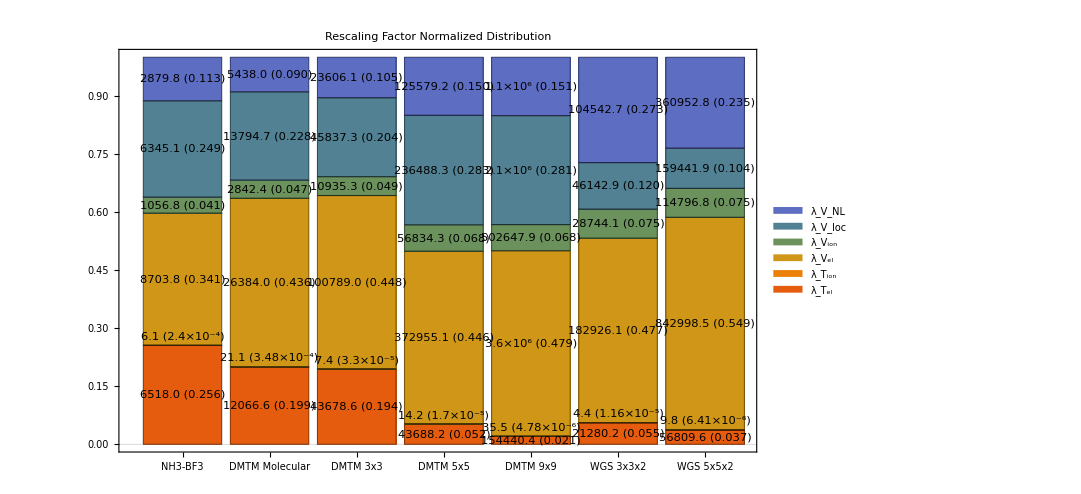

```mathematica
(* Get scaling factor data from all instance results we computed before*)
dataNH3BF3={Instance1Result["exact"]["λTermExact"],Instance1Result["bound"]["λTermBound"]};
dataDMTMSmall={Instance2Result["exact"]["λTermExact"],Instance2Result["bound"]["λTermBound"]};
dataDMTM3={InstanceDMTMClass3Result["exact"]["λTermExact"],InstanceDMTMClass3Result["bound"]["λTermBound"]};
dataDMTM5={InstanceDMTMClass5Result["exact"]["λTermExact"],InstanceDMTMClass5Result["bound"]["λTermBound"]};
dataDMTM9={InstanceDMTMClass9Result["exact"]["λTermExact"],InstanceDMTMClass9Result["bound"]["λTermBound"]};
dataWGS3={InstanceWGSClass3Result["exact"]["λTermExact"],InstanceWGSClass3Result["bound"]["λTermBound"]};
dataWGS5={InstanceWGSClass5Result["exact"]["λTermExact"],InstanceWGSClass5Result["bound"]["λTermBound"]};

allTermData={dataNH3BF3,dataDMTMSmall,dataDMTM3,dataDMTM5,dataDMTM9,dataWGS3,dataWGS5};
exactTermData=First/@allTermData;

totalExactData={Instance1Result["exact"]["λExact"],Instance2Result["exact"]["λExact"],InstanceDMTMClass3Result["exact"]["λExact"],InstanceDMTMClass5Result["exact"]["λExact"],InstanceDMTMClass9Result["exact"]["λExact"],InstanceWGSClass3Result["exact"]["λExact"],InstanceWGSClass5Result["exact"]["λExact"]};

(* Check total rescaling from term based rescaling are all correct *)
checkSum=(Total/@Values/@exactTermData);
totalExactData==checkSum

(* Create figure *)
rescalingFactorDistBarChart=BarChart[Normalize[#,Total]&/@Values/@exactTermData,
ChartLayout->"Stacked",Axes->False,Frame->True,PlotLabel->"Rescaling Factor Normalized Distribution",
ChartLegends->{Style[Subscript["λ",Subscript["T","el"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["T","ion"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","el"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","ion"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","loc"]],14,FontFamily->"Times"],Style[Subscript["λ",Subscript["V","NL"]],14,FontFamily->"Times"]},
LabelingFunction->(Function[{value,index,barPos},If[index[[2]]==2,
Placed[Row[{NumberForm[Values[exactTermData][[index[[1]],index[[2]]]],{Infinity,1}]," (",ScientificForm[value,3],")"}],Above],Placed[Row[{NumberForm[Values[exactTermData][[index[[1]],index[[2]]]],{Infinity,1}]," (",NumberForm[value,{Infinity,3}],")"}],Center]]]),
ChartLabels->{{"NH3-BF3","DMTM Molecular","DMTM 3x3","DMTM 5x5","DMTM 9x9","WGS 3x3x2","WGS 5x5x2"},None},
Epilog->Table[Style[Text[Style[totalExactData[[i]],Black],{i,1.025}],11.5],{i,Length@totalExactData}],
PlotTheme->"Scientific",ImageSize->800,LabelStyle->Directive[FontSize->11.5],FrameStyle->Directive[FontSize->14]]
```

Inside each color bar we show the values of the rescaling factors per term, and in parenthesis the relative contribution to the total rescaling (the λTion bar is negligible, so the corresponding number is at the bottom of the λVel bar). The total rescaling factor is shown on top of each bar stack. We can see that the electron Coulomb terms appear to have the most contribution to the total rescaling factor amount. See Fig. 6.

### Figure 7: Normalized Distribution of 1 Block Encoding Compiling Costs (In # of Toffolis) for Each Problem Instance

Plot the block encoding cost (denoted as compilation cost).

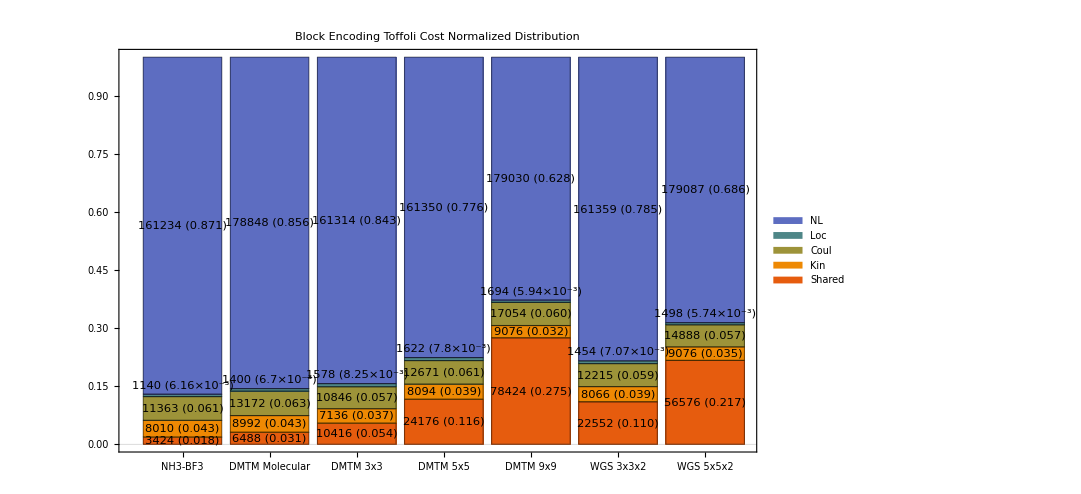

```mathematica
(* Get block encoding data from all instance results we computed before *)
compdataNH3BF3=Instance1Result["compilationCost"];
compdataDMTMSmall=Instance2Result["compilationCost"];
compdataDMTM3=InstanceDMTMClass3Result["compilationCost"];
compdataDMTM5=InstanceDMTMClass5Result["compilationCost"];
compdataDMTM9=InstanceDMTMClass9Result["compilationCost"];
compdataWGS3=InstanceWGSClass3Result["compilationCost"];
compdataWGS5=InstanceWGSClass5Result["compilationCost"];

allcompData={compdataNH3BF3,compdataDMTMSmall,compdataDMTM3,compdataDMTM5,compdataDMTM9,compdataWGS3,compdataWGS5};
breakdownCompData=First/@allcompData;
totalCompData=allcompData[[All,2]];

(* Create figure *)
compilingDistBarChart=BarChart[Normalize[#,Total]&/@breakdownCompData*1.0,
ChartLayout->"Stacked",Axes->False,Frame->True,PlotLabel->"Block Encoding Toffoli Cost Normalized Distribution",
ChartLegends->Map[Style[#,14]&,{"Shared","Kin","Coul","Loc","NL"}],
LabelingFunction->(Function[{value,index,barPos},
If[index[[2]]==4,
Placed[Row[{NumberForm[breakdownCompData[[index[[1]],index[[2]]]],{Infinity,1}]," (",ScientificForm[value,3],")"}],Above],Placed[Row[{NumberForm[breakdownCompData[[index[[1]],index[[2]]]],{Infinity,1}]," (",NumberForm[value,{Infinity,3}],")"}],Center]]]),
ChartLabels->{{"NH3-BF3","DMTM Molecular","DMTM 3x3","DMTM 5x5","DMTM 9x9","WGS 3x3x2","WGS 5x5x2"},None},
Epilog->Table[Style[Text[Style[totalCompData[[i]],Black],{i,1.025}],11.5],{i,Length@totalCompData}],
PlotTheme->"Scientific",ImageSize->800,LabelStyle->Directive[FontSize->11.5],FrameStyle->Directive[FontSize->14]]
```

The numbers inside each color bar indicate the values of the cost for that term and in parenthesis, the relative fraction of the total for that term. The total compilation cost (sum of all global values per term) is shown on top of each bar stack. The numbers above the green bar are for the local term. We can see that the non-local terms appear to have the dominant costs across all instances. See Fig. 7.

### Figure 2: Summary of Total Time Evolution Cost w.r.t. Different Time

We combine the rescaling factor cost and the block encoding cost to form the total time-evolution cost. See Fig. 2.

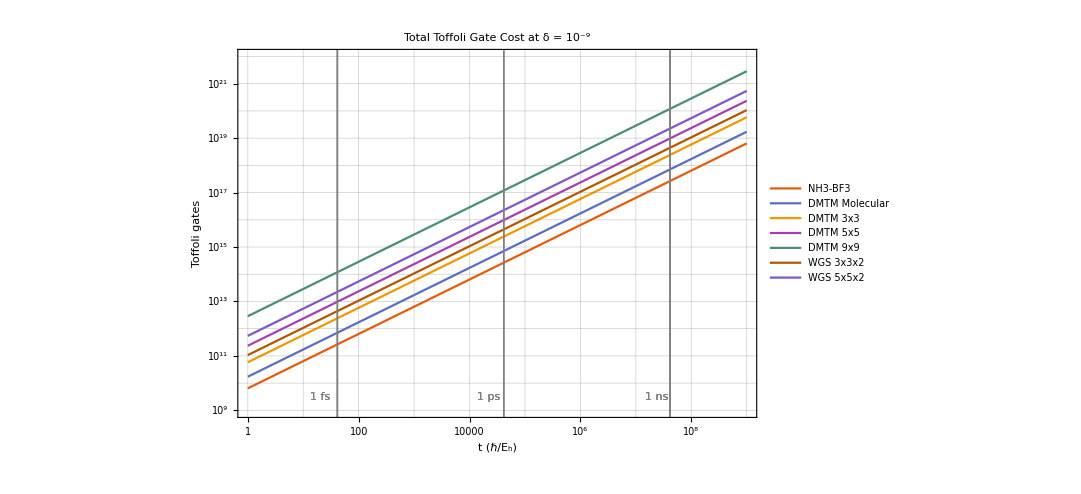

```mathematica
timeLabels={"1 fs", "1 ps", "1 ns"};
timePts={41.34137333517015,41341.373335170145,4.134137333517015*10^7};
timeLabelPts={3,10,17};
δerror=10^-9;
costPlotLine=LogLogPlot[{CostAnalysis`totalCost[Instance1Result,t,δerror,True]["exact"]["total"],CostAnalysis`totalCost[Instance2Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceDMTMClass3Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceDMTMClass5Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceDMTMClass9Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceWGSClass3Result,t,δerror,True]["exact"]["total"],
CostAnalysis`totalCost[InstanceWGSClass5Result,t,δerror,True]["exact"]["total"]},
{t,1,10^9},
PlotLegends->Placed[{"NH3-BF3","DMTM Molecular","DMTM 3x3","DMTM 5x5","DMTM 9x9","WGS 3x3x2","WGS 5x5x2"},{0.72,0.25}],
Ticks->{Table[10^i,{i,0,6}],Table[10^i,{i,9,18}] },
Frame->True,FrameLabel->{Row[{"t (",ℏ,"/",Subscript[Style["E",Italic],"h"],")"}],"Toffoli gates"},PlotRange->{{1,10^9},{10^9,10^22}},
GridLines->All,
PlotLabel->"Total Toffoli Gate Cost at δ = 10^-9",Epilog->{Thick,Gray,Table[{InfiniteLine[{{Log[x],0},{Log[x],1}}],Style[Text[Style[timeLabels[[i]],Gray],{timeLabelPts[[i]],Log@(10^9.5)}],14]},{x,timePts},{i,1,3}]},PlotTheme->"Scientific",ImageSize->800,LabelStyle->Directive[FontSize->14],TicksStyle->Directive[FontSize->14],Exclusions->None]
```

You can also export these figures as pdf files if needed.

```mathematica
(* Export figs *)
(*SetDirectory["..."]
Export["rescalingFactorDist.pdf",rescalingFactorDistBarChart]
Export["compilingDist.pdf",compilingDistBarChart]
Export["timeEvoCost.pdf",costPlotLine]*)
```